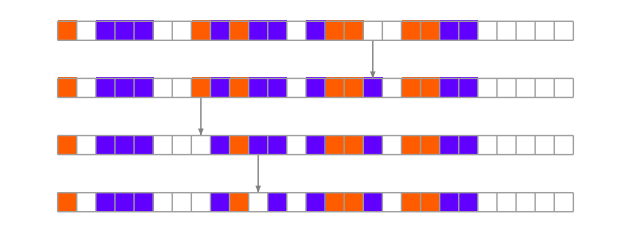

```mathematica
Module[
{deep=100,cut=200,ru,life},
SeedRandom[5000+53];
{{"[◼]", "RulesMutationPlot"}}[
Take[First/@Split[First/@NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]
],{48,51}]]]
```

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
e3 = Module[
{deep=5000,cut=200,ru,life},
SeedRandom[5000+53];
NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]];
```

```mathematica
evo=Map[DeleteDuplicates,SplitBy[e3,Last]];
```

```mathematica
res=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,20(Length[data]+1)^.7},
Mesh->True,MeshStyle->Opacity[.1] ]]&,
evo,{2}];
```

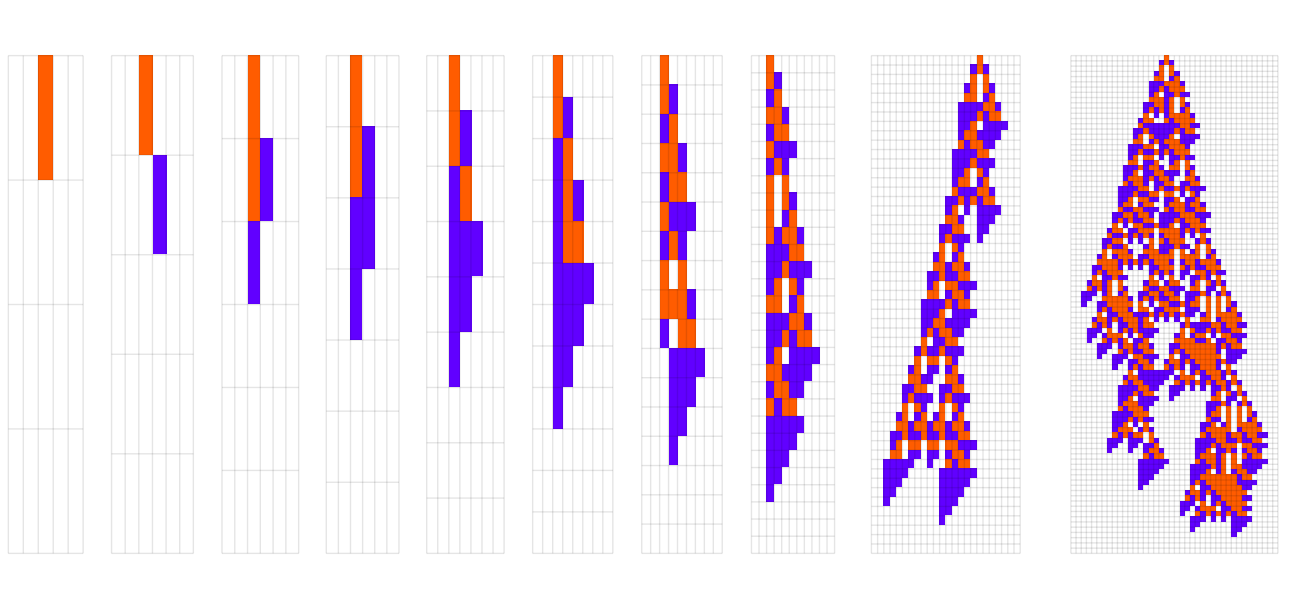

```mathematica
GraphicsRow[First/@Rest[res]]
```

```mathematica
Module[{
seed=5000+53,k=3,r=1,cut=200,deep=5000,fun=Length,
init,evo,ru,data,lt,test,mask,canonical,res},
If[Not[TrueQ[seed]],SeedRandom[seed]];
init=FromDigits[Lookup[Association[Thread[Append[
Permutations[CenterArray[1,2r+1]],
CenterArray[0,2r+1]]->1]],{{"[◼]", "RuleTuples"}}[k,r],0],2];
init={0,{0,init},1,fun[{{1}}]};
evo=NestList[Function[item,
ru=First[{{"[◼]", "RandomRuleMutation"}}[{First[item],k,r}]];
data=CellularAutomaton[{ru,k,r},{{1},0},{cut,All}];
lt=If[SameQ[#,0],True,cut-#+1]&[
LengthWhile[Reverse[data],Total[#]==0&]];
If[TrueQ[lt],item,
test=fun[{{"[◼]", "MatrixCrop"}}[data]];
If[test<Last[item],item,
data=Union[Catenate[Partition[#,2r+1,1]&/@data]];
mask=Lookup[Association[Thread[data->1]],{{"[◼]", "RuleTuples"}}[k,r],0];
canonical=IntegerDigits[ru,k,k^(2r+1)];
canonical={FromDigits[canonical*mask,k],
FromDigits[mask,2]};
{ru,canonical,lt,test}
]]],init,deep];
evo=Map[Rest@*First,SplitBy[evo,#[[2]]&]];
evo=Map[DeleteDuplicates,SplitBy[evo,Last]];
res=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,20(Length[data]+1)^.7},
Mesh->True,MeshStyle->Opacity[.1] ]]&,
evo,{2}];
GraphicsRow[First/@res]
]
```

$Aborted

```mathematica
Module[{
k=3,r=1,cut=200,deep=5000,fun=Length,
init,evo,ru,data,lt,test,mask,canonical,res},
res=ParallelTable[SeedRandom[seed];
init=FromDigits[Lookup[Association[Thread[Append[
Permutations[CenterArray[1,2r+1]],
CenterArray[0,2r+1]]->1]],{{"[◼]", "RuleTuples"}}[k,r],0],2];
init={0,{0,init},1,fun[{{1}}]};
evo=NestList[Function[item,
ru=First[RandomRuleMutation[{First[item],k,r}]];
data=CellularAutomaton[{ru,k,r},{{1},0},{cut,All}];
lt=If[SameQ[#,0],True,cut-#+1]&[
LengthWhile[Reverse[data],Total[#]==0&]];
If[TrueQ[lt],item,
test=fun[{{"[◼]", "MatrixCrop"}}[data]];
If[test<Last[item],item,
data=Union[Catenate[Partition[#,2r+1,1]&/@data]];
mask=Lookup[Association[Thread[data->1]],{{"[◼]", "RuleTuples"}}[k,r],0];
canonical=IntegerDigits[ru,k,k^(2r+1)];
canonical={FromDigits[canonical*mask,k],
FromDigits[mask,2]};
{ru,canonical,lt,test}
]]],init,deep];
evo=Map[Rest@*First,SplitBy[evo,#[[2]]&]];
evo=Map[DeleteDuplicates,SplitBy[evo,Last]];
res=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,20(Length[data]+1)^.7}]]&,
evo,{2}];
Map[First,res]
,
{seed,5000+{54,60}}];
GraphicsColumn[
Map[GraphicsRow,res]
]
]
```

-Graphics-

```mathematica
evolutionGraph=VertexOutComponentGraph[{{"[◼]", "EvolutionaryMultiwayGraph"}}[
{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],
"Reduced"->False,
GraphLayout->"LayeredDigraphEmbedding",
"DistanceFunction"->{{"[◼]", "BinaryMutationDistance"}},
AspectRatio->1],{{0,65815}}];
```

```mathematica
evolutionEdges=GroupBy[Join[
Flatten[Map[Outer[Rule,#,#,1]&,
VertexList[evolutionGraph]],2],
Flatten[MapApply[Outer[Rule,#1,#2,1]&,
EdgeList[evolutionGraph]],2]],First->Last];
```

```mathematica
lftdata=KeyMap[First,{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"]];
dataCallouts={{"[◼]", "quickDepict"}}[{2,2},{#,0},lftdata[#]]&/@VertexList[evolutionGraph][[All,1,1]];
```

```mathematica
rules={{"[◼]", "AllSymetricQuiescentRules"}}[2,2];
```

```mathematica
gensIndex=First/@PositionIndex[Union@@evolutionEdges];
```

```mathematica
gensRuleMap=AssociationMap[{{"[◼]", "GenRulesSymmetric"}}[{2,2},#]&,Keys[gensIndex]];
```

```mathematica
gensRuleIndex=Map[{{"[◼]", "SymmetricEncode"}},gensRuleMap,{2}]/2+1;
```

```mathematica
gensRuleIndices=Catenate@Lookup[gensRuleIndex,#]&/@VertexList[evolutionGraph];
```

```mathematica
ruleGensMap=Association@Catenate@KeyValueMap[{g,rs}|->#->Lookup[gensIndex,Key[g]]&/@rs,gensRuleMap];
```

```mathematica
evolutionEdgesIndex=Lookup[gensIndex,#]&/@KeyMap[gensIndex]@evolutionEdges;
```

```mathematica
(*MarkovWeights=SparseArray[Map[rule|->With[{
idx=Lookup[evolutionEdgesIndex,ruleGensMap[rule]],
mutations={{"[◼]", "RuleMutationsList"}}[{rule,2,2},"Symmetric"->True][[All,1]]
},
SparseArray[
With[
{allowedMutations=Select[mutations,MemberQ[idx,ruleGensMap[#]]&]},
Append[{{"[◼]", "SymmetricEncode"}}[rule]/2+1->Length[mutations]-Length[allowedMutations]]@Thread[({{"[◼]", "SymmetricEncode"}}/@allowedMutations)/2+1->1
]
]
,
Length[rules]
]
],rules]];//AbsoluteTiming*)
```

```mathematica
MarkovWeights=Import[CloudObject[["https://www.wolframcloud.com/obj/6a379236-239e-4d1b-b04d-f41ae480d106"](https://www.wolframcloud.com/obj/6a379236-239e-4d1b-b04d-f41ae480d106)]];
```

```mathematica
rulesMarkovMatrix=N[MarkovWeights/Total/@MarkovWeights];
```

```mathematica
data=Transpose[(d|->Total@d[[#]]&/@gensRuleIndices)/@NestList[#.rulesMarkovMatrix&,UnitVector[Length[rules],1],1500]];
```

```mathematica
Block[{data=data[[All,;;1500]],n1=7,n2=4,x=300,ordering1,ordering2},
ordering1=Reverse@Ordering@data[[All,-1]];
ordering2=Reverse@Ordering@data[[ordering1,x]];
StackedListPlot[data[[ordering1]],Epilog->Reverse@Join[
MapThread[Inset[#1,{Length[data[[1]]]0.95,#2},Automatic,Scaled[.07]]&,{dataCallouts[[ordering1[[;;n1]]]],Mean/@Partition[Prepend[0]@Accumulate[data[[ordering1]][[;;n1,-1]]],2,1]}]
,
MapThread[Inset[#1,{x,#2},Automatic,Scaled[.07]]&,{dataCallouts[[ordering1[[ordering2]][[;;n2]]]],Mean/@Partition[Prepend[0]@Accumulate[data[[ordering1,x]]],2,1][[ordering2[[;;n2]]]]}]
]
]
]
```

-Graphics-